### Header

Project 			: 	EPFL demonstrations Notebooks
Author			: 	Amina Matt
Date created 		:	November 2018
Purpose			: 	Illustrate the Lever rule
Revision history	:	“Index” in nearest is an update from version 11.1

# Level (i) and (ii)

To run the code on a Macintosh use successively ⌘+A and ⇧+↵ . It should take around 5 seconds before a new window appear.

## Generalization of an eutectic phase diagram

## Phase diagram construction

### Variables definitions

```mathematica
(*quadratic coefficient*)
a01=50;
a02=RandomReal[{2,2.5}]*a01;
a03=a02;
a04=RandomReal[{2,2.5}]*a01;
(*linear coefficient*)
b01=50;
b02=RandomReal[{2,2.5}]*b01;
b03=b02;
b04=RandomReal[{1,1.25}]*b01;
(*abscisses*)
c01=50;
c02=RandomReal[{1,1}]*c01;
c03=RandomReal[{1.1,1.1}]*c01;
c04=RandomReal[{1.25,1.55}]*c01;
```

### Functions definitions

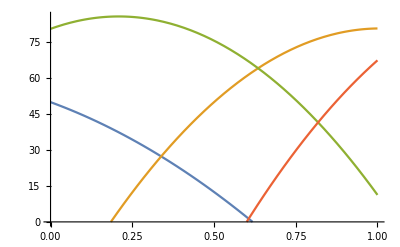

```mathematica
liquidus1[composition_]:=-a01 (composition+1)^2+b01 (composition+1)+c01;(*On the extreme left*)
liquidus2[composition_]:=-a02 (composition-0.5)^2+b02 (composition-0.5)+c02;(*Cross the liquidus 1*)
liquidus3[composition_]:=-a03 (composition+0.3)^2+b03( composition+0.3)+c03;(*Cross the liquidus 2*)
liquidus4[composition_]:=-a02 (composition-1)^2+b02 (composition-1)+c04;(*On the extreme right*)
Plot[{liquidus1[comp],liquidus2[comp],liquidus3[comp],liquidus4[comp]},{comp,0,1},PlotRange->{{0,1},{0,Automatic}}]
```

### Analysis of the phase diagram - points of interest

```mathematica
listLiquidus={liquidus1,liquidus2,liquidus3,liquidus4};
listVerticales={0,intersection,1}; 
listVerticalesPhases={alpha,intermetallic,beta};
allPhases=Catenate[{listLiquidus,listVerticalesPhases}];
(*First eutectic, i.e. intersection of two liquidus lines*)
eutecticComp1=Solve[liquidus1[c]==liquidus2[c] && 0≤c≤1,c][[1,1,2]];
eutecticTemperature1=liquidus1[eutecticComp1];
(*Second eutectic*)
eutecticComp2=Solve[liquidus3[c]==liquidus4[c]&&0≤  c≤1,c][[1,1,2]];
eutecticTemperature2=liquidus3[eutecticComp2];
(*Intermetallic*)
intersection=Solve[liquidus2[c]==liquidus3[c]&&0≤  c≤1,c][[1,1,2]];intersectionTemperature=liquidus3[intersection];
```

#### Comment : The eutectic is the composition of a mixture of two phases or more that has a melting point lower than the fusion temperature of each component.

## Functions

### Intersection between an isotherm (i.e. line of constant temperature) and the liquidi

```mathematica
equivalentCompLiquidusTemp::usage="Find the intersection between the isotherm given by in argument and each liquidus";
```

```mathematica
equivalentCompLiquidusTemp[chosenTemp_]:={
N@Solve[liquidus1[equivalentComp]==chosenTemp &&0≤ equivalentComp≤ eutecticComp1,equivalentComp],
N@Solve[liquidus2[equivalentComp]==chosenTemp &&eutecticComp1< equivalentComp≤ intersection,equivalentComp],
N@Solve[liquidus3[equivalentComp]==chosenTemp &&intersection< equivalentComp ≤eutecticComp2,equivalentComp],
N@Solve[liquidus4[equivalentComp]==chosenTemp &&eutecticComp2< equivalentComp≤ 1,equivalentComp]
};
```

## Graphic Style

#### Color scheme

```mathematica
myBlue=LightBlue (*Blend[{Blue,White},0.85]*);
mylightPurple=Blend[{LightBlue,Purple},0.5];
mylightRed=Blend[{LightBlue,Red},0.5];
mylightBlue=Blend[{LightBlue,Blue},0.5];
```

#### Legends

```mathematica
legends=Module[{mysize=14},{
Style[Text["α - Solid α"],mysize,Purple],
Style[Text["α+L - Solid α+liquid"],mysize,mylightPurple],
Style[Text["L - Liquid"],mysize,Black],
Style[Text["L+M - Liquid+Intermetallic"],mysize,mylightRed],
Style[Text["M - Intermetallic"],mysize,Red],
Style[Text["M+L - Intermetallic+Liquid"],mysize,mylightRed],
Style[Text["L+β - Liquid+Solid β"],mysize,mylightBlue]
,Style[Text["β - Solid β"],mysize,Blue],
Style[Text["α+M - Solid α+Intermetallic"],mysize,GrayLevel[0.50]],
Style[Text["M+β - Intermetallic+Solid β"],mysize,GrayLevel[0.70]]}//TableForm];
```

## Regions definitions for lever rule

### Biphasic Regions

#### Definitions

```mathematica
(*The parametrization could also be done with RegionPlot*)
```

```mathematica
solidalphaliquid=Region[ParametricRegion[{comp,eutecticTemperature1+t(liquidus1[comp]-eutecticTemperature1) },{{comp,0,eutecticComp1},{t,0,1}}],PlotRange-> {{0,1},{0,80}},BaseStyle-> Directive[{mylightPurple}],Frame->True,ImageSize->Medium,FrameLabel-> {"Composition","Temperature"},FrameStyle->Directive[Thin,Black,14]];solidalphaliquidDomain=DiscretizeRegion@solidalphaliquid;
```

```mathematica
liquidIntermetallic=Region[ParametricRegion[{comp,eutecticTemperature1+t(liquidus2[comp]-eutecticTemperature1) },{{comp,eutecticComp1,intersection},{t,0,1}}],BaseStyle-> Directive[{mylightRed}]];
liquidIntermetallicDomain= DiscretizeRegion@liquidIntermetallic;
```

```mathematica
intermetallicLiquid=Region[ParametricRegion[{comp,eutecticTemperature2+t(liquidus3[comp]-eutecticTemperature2) },{{comp,intersection,eutecticComp2},{t,0,1}}],BaseStyle-> Directive[{mylightRed}]];
```

```mathematica
intermetallicLiquidDomain=DiscretizeRegion@intermetallicLiquid;
```

```mathematica
liquidSolidBeta=Region[ParametricRegion[{comp,eutecticTemperature2+t(liquidus4[comp]-eutecticTemperature2) },{{comp,eutecticComp2,1},{t,0,1}}],BaseStyle-> Directive[{mylightBlue}]];
```

```mathematica
liquidSolidBetaDomain=DiscretizeRegion@liquidSolidBeta;
```

```mathematica
solidalphaIntermetallic=Graphics[{Gray,Rectangle[{0,0},{intersection,eutecticTemperature1}]}];
```

```mathematica
solidalphaIntermetallicDomain=DiscretizeGraphics@solidalphaIntermetallic;
```

```mathematica
intermetallicSolidBeta=Graphics[{LightGray,Rectangle[{intersection,0},{1,eutecticTemperature2}]}];
```

```mathematica
intermetallicSolidBetaDomain=DiscretizeGraphics@intermetallicSolidBeta;
```

```mathematica
list=<|
"Liquid"->myBlue,
"Solid α"->Purple,
"Solid β"->Blue,
"Intermetallic"->Red|>;
```

```mathematica
regionTest[point_:{px_,py_}]:=Which[(*phase, left(color),right,*)
RegionMember[liquidRegionDomain,point],{"L","Liquid", "Liquid"},
RegionMember[solidalphaliquidDomain,point],{"α+L", "Solid α","Liquid"},
RegionMember[liquidIntermetallicDomain,point],{"L+M","Liquid","Intermetallic"},
RegionMember[intermetallicLiquidDomain,point],{"M+L","Intermetallic","Liquid"},
RegionMember[solidalphaIntermetallicDomain,point],{"α+M","Solid α","Intermetallic"},
RegionMember[intermetallicSolidBetaDomain,point],{"M+β","Intermetallic","Solid β"}
]
```

#### Legends

```mathematica
legendsAbbBi=Graphics[{
Text[Style["α+L",Medium,White],{eutecticComp1/2,eutecticTemperature1+(liquidus1[eutecticComp1/2]-eutecticTemperature1)/2}],
Text[Style["L+M",Medium,White],
{eutecticComp1+((intersection-eutecticComp1)/2),eutecticTemperature1+(liquidus2[eutecticComp1+((intersection-eutecticComp1)/2)]-eutecticTemperature1)/2}],
Text[Style["M+L",Medium,White],{intersection+((eutecticComp2-intersection)/2),eutecticTemperature2+(liquidus3[intersection+((eutecticComp2-intersection)/2)]-eutecticTemperature2)/2}],
Text[Style["L+β",Medium,White],{eutecticComp2+((1-eutecticComp2)/2),eutecticTemperature2+(liquidus4[eutecticComp2+((1-eutecticComp2)/2)]-eutecticTemperature2)/2}],
Text[Style["α+M",Medium,White],{intersection/2,eutecticTemperature1/2}],
Text[Style["M+β",Medium,White],{intersection+((1-intersection)/2),eutecticTemperature2/2}]
}
];
```

#### Graphic

```mathematica
allBiphasic=Show[solidalphaliquid,liquidIntermetallic,intermetallicLiquid,liquidSolidBeta,solidalphaIntermetallic,intermetallicSolidBeta,legendsAbbBi
,AspectRatio->1/GoldenRatio,Background->Transparent,ImageSize->500];
```

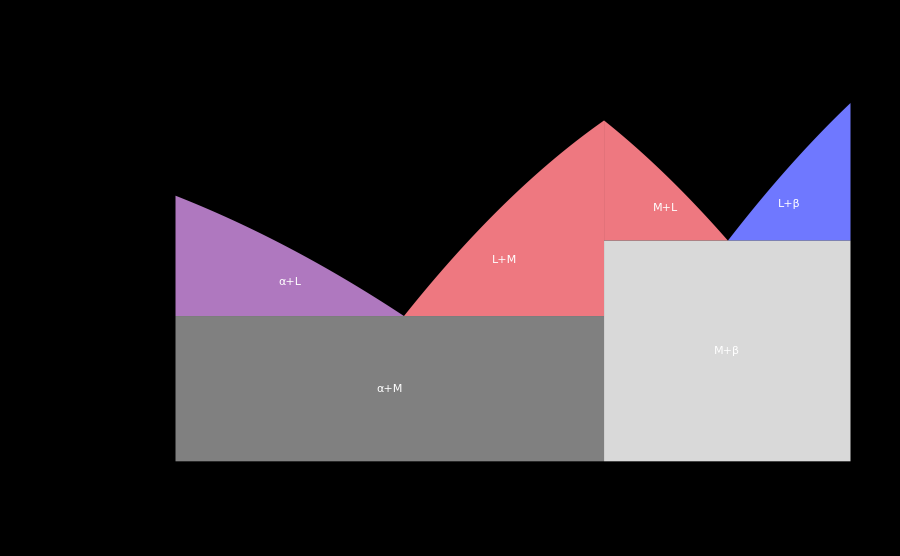

```mathematica
allBiphasicWithLegends=Show[solidalphaliquid,liquidIntermetallic,intermetallicLiquid,liquidSolidBeta,solidalphaIntermetallic,intermetallicSolidBeta,legendsAbbBi
,AspectRatio->1/GoldenRatio,Background->Transparent,ImageSize->900]
```

### Invariants

#### Definitions

```mathematica
eutectic1Region=Graphics[Line[{{0,eutecticTemperature1},{intersection,eutecticTemperature1}}],PlotRange-> {{0,1},{0,80}},Frame->True,ImageSize->Medium,FrameLabel-> {"Composition","Temperature"},FrameStyle->Directive[Thin,Black,14]];
eutectic2Region=Graphics[{GrayLevel[0.75],Line[{{intersection,eutecticTemperature2},{1,eutecticTemperature2}}]}];
eutectic1Point=Graphics[{GrayLevel[0.5],PointSize[0.03],Point[{eutecticComp1,eutecticTemperature1}]}];
eutectic2Point=Graphics[{GrayLevel[0.75],PointSize[0.03],Point[{eutecticComp2,eutecticTemperature2}]}];
```

#### Legends

```mathematica
legendsInvariants=Graphics[{
Text[Style["Eutectic\n L→α+M",Medium,Black],{eutecticComp1,eutecticTemperature1+10}],Text[Style["Eutectic\n L→β+M",Medium,Black],{eutecticComp2,eutecticTemperature2+10}]}];
```

#### Graphic

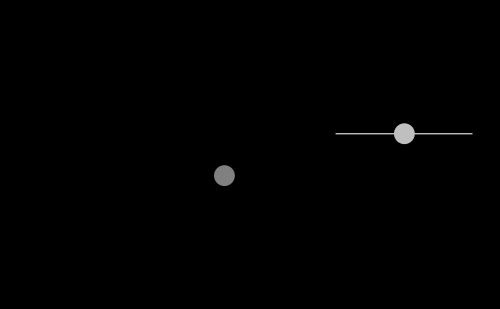

```mathematica
invariants=Show[eutectic1Region,eutectic2Region,eutectic1Point,eutectic2Point,legendsInvariants,ImageSize->500,AspectRatio-> 1/GoldenRatio,Background->Transparent]
```

### Monophasic Regions

#### Definition

```mathematica
allLiquidus[comp_]:=Piecewise[{
{liquidus1[comp],0<comp<eutecticComp1},
{liquidus2[comp],eutecticComp1<comp<intersection},
{liquidus3[comp],intersection<comp<eutecticComp2},
{liquidus4[comp],eutecticComp2<comp<1}}]
```

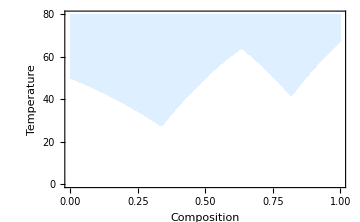

```mathematica
liquidRegion=RegionPlot[80>y>allLiquidus[x]&&0<x<1,{x,0,1},{y,0,100},MaxRecursion->5,PlotRange-> {{0,1},{0,80}},PlotStyle-> LightBlue,Frame->True,ImageSize->Medium,BoundaryStyle->None,FrameLabel-> {"Composition","Temperature"},FrameStyle->Directive[Thin,Black,14],AspectRatio->1/GoldenRatio]
```

```mathematica
liquidRegionDomain=DiscretizeGraphics@liquidRegion;
```

```mathematica
(*liquidRegion=Plot[allLiquidus[comp],{comp,0,1},PlotRange-> {{0,1},{0,80}},PlotStyle-> LightBlue,Filling->Top,FillingStyle->Directive[LightBlue],Frame->True,ImageSize->Medium,FrameLabel-> {"Composition","Temperature"},FrameStyle->Directive[Thin,Black,14],AspectRatio->1/GoldenRatio]*)
```

```mathematica
solidAlpha=Graphics[{Red,Thickness[t1],Line[{{intersection,0},{intersection,intersectionTemperature}}]}];
intermetallic=Graphics[{Blue,Thickness[t2],Line[{{1,0},{1,liquidus4[1]}}]}];
solidBeta=Graphics[{Purple,Thickness[t2],Line[{{0,0},{0,liquidus1[0]}}]}];
```

#### Legends

```mathematica
legendsAbbMono=Graphics[{
Text[Style["← α",Medium,Purple],{0.1,eutecticTemperature1}],
Text[Style["L",Medium,Black],
{eutecticComp1,eutecticTemperature1+20}],
Text[Style["← M",Medium,Red],{intersection+((eutecticComp2-intersection)/2),eutecticTemperature1}],
Text[Style["β →",Medium,Blue],{0.9,eutecticTemperature1}]
}
];
legendsAbbMonoClose=Module[{hight=eutecticTemperature1-5},
Graphics[{
Text[Style["α",Medium,Purple],{0.02,hight}],
Text[Style["L",Medium,Black],
{eutecticComp1,hight+20}],
Text[Style["M",Medium,Red],{intersection+0.02,hight}],
Text[Style["β",Medium,Blue],{0.98,hight}]
}
]];
```

#### Graphic

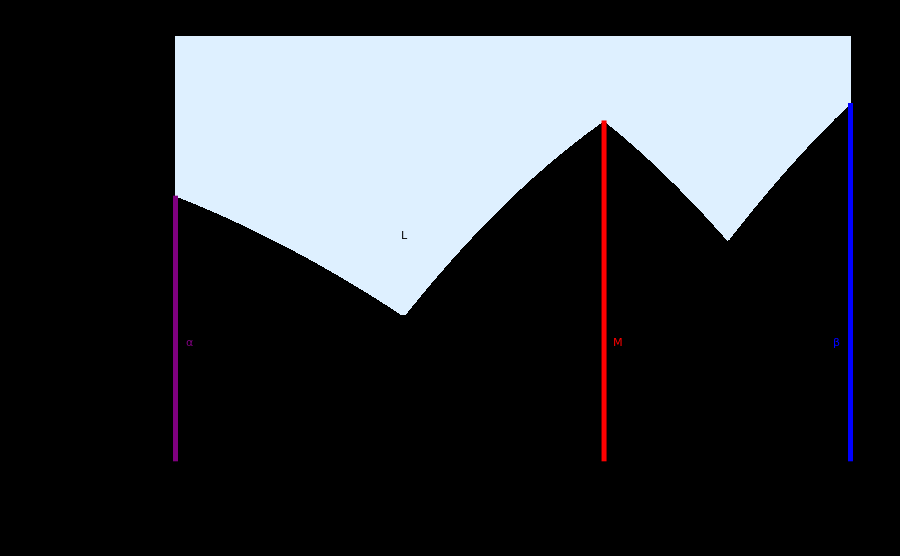

```mathematica
allMonophasic=Show[liquidRegion,solidAlpha,intermetallic,solidBeta,legendsAbbMono,Background->Transparent,ImageSize-> 500]/.{t1-> 0.010,t2-> 0.015};
allMonophasicWithLegend=Show[liquidRegion,solidAlpha,intermetallic,solidBeta,legendsAbbMonoClose,ImageSize-> 900,Background->Transparent]/.{t1-> 0.004,t2-> 0.004}
```

```mathematica
allMonophasicWithLegend,ImageSize->Large]
```

#### Background

```mathematica
imagebck=
Show[Graphics[{Transparent,Rectangle[]}],ImageSize->500,AspectRatio->1/GoldenRatio];
```

## Animation

```mathematica
biphasic=False;
```

```mathematica
question1=Panel[
DynamicModule[{x=Null},
Grid[{{Style["EXERCISE\n",20]},{Style["How many biphasic domains are on this diagram?",16],
InputField[Dynamic[x]],Style[Dynamic[x==6],16]}},Alignment->Left]
]];
```

```mathematica
window=
CreateDocument[{
Manipulate[
DynamicModule[
(*local variables*)
{c,chosenComp,chosenTemp,equivalentCompLiquidusTempVal,equivalentCompLiquidus,allEquivalentComp,distances,first,second,curvePositionVal,d,curvePosition,equivalentCompOfInterest,totalComp,diffComp1,diffComp2,fraction1,fraction2,infos,phaseOfInterest},
(*variables definitions*)
{chosenComp,chosenTemp}=point;
(*call to function for isotherme*)
equivalentCompLiquidusTempVal=equivalentCompLiquidusTemp[chosenTemp];
(*Finding neighboring phases*)
equivalentCompLiquidus=If[Length@#>0,#[[1,1,2]],1000]&/@equivalentCompLiquidusTempVal;
allEquivalentComp=Catenate[{equivalentCompLiquidus,listVerticales}];
distances=(chosenComp-#)&/@allEquivalentComp;
first=TakeSmallest[Cases[distances, x_/;x>0],1];
second=TakeLargest[Cases[distances, x_/;x<0],1];
curvePositionVal=Catenate[{first,second}];
curvePosition=Position[distances,#][[1,1]]&/@curvePositionVal;
equivalentCompOfInterest=(allEquivalentComp[[#]]&/@curvePosition);
(*Values for lever rule calculation*)
totalComp=Abs@(equivalentCompOfInterest[[1]]-equivalentCompOfInterest[[2]]);
{diffComp1,diffComp2}=(chosenComp-(allEquivalentComp[[#]]&/@curvePosition));
{fraction1,fraction2}={diffComp1,diffComp2}/totalComp;
infos=regionTest[point];(*phase, left-phase, right-phase*)
d=1.5;(*decalage*)
(*Lever rule graphic*)
fraction=
Graphics[{
(*phase1*){list[infos[[2]]],Rectangle[{0+d,0},{1+d-Abs@fraction1,1}]},
(*phase2*){list[infos[[3]]],Rectangle[{(1+d-Abs@fraction1),0},{1+d,1}]},
If[infos[[2]]==infos[[3]],Text[Style[StringJoin[infos[[2]],"→"],Medium,Black],{-0.15+d,0.5}],
{Inset[NumberForm[(1-fraction1),{1,2}],{0.2+d,-0.1}],
Inset[NumberForm[fraction1,{1,2}],{0.7+d,-0.1}],
Text[Style[StringJoin[infos[[2]],"→"],Medium,Black],{-0.15+d,0.5}],
Text[Style[StringJoin["←",infos[[3]]],Medium,Black],{1.15+d,0.5}]}]
},ImageSize->Medium];
(*Large phase diagram graphic*)
phaseOfInterest=(allPhases[[#]]&/@curvePosition);
(*test=*)Grid[{{},{
Show[allBiphasicWithLegends,allMonophasicWithLegend,
If[infos[[2]]==infos[[3]],imagebck,Show[{
Graphics@Point[point],
Graphics[{Thick,list[infos[[2]]],Line[{{equivalentCompOfInterest[[1]],chosenTemp},{chosenComp,chosenTemp}}]}],
Graphics[{Dotted,Thick, list[infos[[2]]],Line[{{equivalentCompOfInterest[[1]],0},{equivalentCompOfInterest[[1]],chosenTemp}}]}],
Graphics[{Thick, list[infos[[3]]],Line[{{chosenComp,chosenTemp},{equivalentCompOfInterest[[2]],chosenTemp}}]}],
Graphics[{Dotted,Thick, list[infos[[3]]],Line[{{equivalentCompOfInterest[[2]],0},{equivalentCompOfInterest[[2]],chosenTemp}}]}]}
,(*Epilog->Inset[Abs@fraction1],*)Frame->True,FrameLabel-> {"Composition","Temperature"},
FrameStyle->Directive[Thin,Black,14]]]],
legends
}}]],
{{point,{0.1,40}},Locator,LocatorRegion->{{0,1},{0,50}}},
Delimiter,
(*Small modular phase diagram graphics*)
{{phaseNumberFlag,{image-> imagebck},"Number of Phases"},
{{image-> invariants}-> "Invariants",
{image-> allMonophasic}-> "Monophasic",
{image-> allBiphasic}-> "Biphasic"}},
Delimiter,Dynamic[image /.phaseNumberFlag],Delimiter,Dynamic[fraction],
ControlPlacement->{Left},LabelStyle->{16}],question1},WindowSize-> All,ShowCellBracket->False];
```